```mathematica
(*Quit[]*)
Clear["Global`*"]
```

Antagonistic Specialization Adaptive Dynamics. We begin by defining the change in frequency of each strategist type over time:

```mathematica
(*To begin we first define the payoffs received by hosts and symbionts*)
(*x -> the proportion of a host's resource that is shared*)
(*α -> the matched exchange rate*)
(*αg -> the generalist exchange rate*)
(*γ -> the efficiency of exchange, monotypic*)
pi=x*(α*γ−x); (*Host matched payoff*)
pi2=x*(fα*γ−x);(*Host mis-matched payoff*)
pig=x*(αg*γ−x);(*Generalist host payoff*)
ψ=x*γ*(1−α);(*Symbiont matched payoff*)
ψ2=x*γ*(1−fα);(*Host mis-matched payoff*)
ψg=x*γ*(1−αg); (*Symbiont payoff from interaction with generalist host*)
```

In the fitness feedback model, the average host and symbiont payoffs are proportional to the payoffs received by the symbiont that partners with them:

```mathematica
(*v1 = frequency of host 1*)
(*v2 = frequency of host 2*)
WS1 = v1*ψ*pi^b+v2*ψ2*pi2^b+(1-v1-v2)*ψg*pig^b;
WS2 = v1*ψ2*pi2^b+v2*ψ*pi^b+(1−v1−v2)*ψg*pig^b;

WH1=u*pi*ψ^b+(1-u)*pi2*ψ2^b;(*Host 1 Average Payoff*)
WH2 = u*pi2*ψ2^b+(1−u)*pi*ψ^b;(*Host 2 Average Payoff*)
WHG = pig*ψg^b;(*Generalist Host Average Payoff*)

Sbar = u*WS1+(1-u)*WS2 ;(*Average Payoff of a randomly chosen symbiont*)
Hbar = v1*WH1+v2*WH2+(1-v1-v2)(WHG)(*Average Payoff of a randomly chosen host*)
```

(1-v1-v2) x (x (1-αg) γ)^b (-x+αg γ)+v2 (u x ((1-fα) x γ)^b (-x+fα γ)+(1-u) x (x (1-α) γ)^b (-x+α γ))+v1 ((1-u) x ((1-fα) x γ)^b (-x+fα γ)+u x (x (1-α) γ)^b (-x+α γ))

Find the frequencies of hosts and symbionts over time:

```mathematica
S =u*(WS1-Sbar);
S=Simplify[S] ;(*Change in Symbiont Frequency over time*)
S/.{v1->v1[t],v2-> v2[t],u-> u[t]}
```

x γ (-(x (-x+fα γ))^b+fα (x (-x+fα γ))^b+(x (-x+α γ))^b-α (x (-x+α γ))^b) (-1+u[t]) u[t] (-v1[t]+v2[t])

```mathematica
(*u = frequency of symbiont 1*)
V1=v1*(WH1-Hbar);(*Change in Host 1 frequency over time*)
V1=Simplify[V1];
V1/.{v1->v1[t],v2-> v2[t],u-> u[t]}
V2=v2*(WH2-Hbar);(*Change in Host 2 frequency over time*)
V2=Simplify[V2];
V2/.{v1->v1[t],v2-> v2[t],u-> u[t]}
```

v1[t] (x (-(-1+fα) x γ)^b (x-fα γ) (-1+u[t])+x (-x (-1+α) γ)^b (-x+α γ) u[t]-(x (-(-1+fα) x γ)^b (x-fα γ) (-1+u[t])+x (-x (-1+α) γ)^b (-x+α γ) u[t]) v1[t]-(x (-x (-1+α) γ)^b (x-α γ) (-1+u[t])+x (-(-1+fα) x γ)^b (-x+fα γ) u[t]) v2[t]-x (-x (-1+αg) γ)^b (x-αg γ) (-1+v1[t]+v2[t]))

v2[t] (x (-x (-1+α) γ)^b (x-α γ) (-1+u[t])+x (-(-1+fα) x γ)^b (-x+fα γ) u[t]-(x (-(-1+fα) x γ)^b (x-fα γ) (-1+u[t])+x (-x (-1+α) γ)^b (-x+α γ) u[t]) v1[t]-(x (-x (-1+α) γ)^b (x-α γ) (-1+u[t])+x (-(-1+fα) x γ)^b (-x+fα γ) u[t]) v2[t]-x (-x (-1+αg) γ)^b (x-αg γ) (-1+v1[t]+v2[t]))

Next, I type this system up dynamically for subsequent simulations:

```mathematica
ANT[α_,αg_,fα_,γ_,x_,b_]:= {u'[t]==x γ (-(x (-x+fα γ))^b+fα (x (-x+fα γ))^b+(x (-x+α γ))^b-α (x (-x+α γ))^b) (-1+u[t]) u[t] (-v1[t]+v2[t]),v1'[t]== v1[t] (x (-(-1+fα) x γ)^b (x-fα γ) (-1+u[t])+x (-x (-1+α) γ)^b (-x+α γ) u[t]-(x (-(-1+fα) x γ)^b (x-fα γ) (-1+u[t])+x (-x (-1+α) γ)^b (-x+α γ) u[t]) v1[t]-(x (-x (-1+α) γ)^b (x-α γ) (-1+u[t])+x (-(-1+fα) x γ)^b (-x+fα γ) u[t]) v2[t]-x (-x (-1+αg) γ)^b (x-αg γ) (-1+v1[t]+v2[t])),v2'[t]== v2[t] (x (-x (-1+α) γ)^b (x-α γ) (-1+u[t])+x (-(-1+fα) x γ)^b (-x+fα γ) u[t]-(x (-(-1+fα) x γ)^b (x-fα γ) (-1+u[t])+x (-x (-1+α) γ)^b (-x+α γ) u[t]) v1[t]-(x (-x (-1+α) γ)^b (x-α γ) (-1+u[t])+x (-(-1+fα) x γ)^b (-x+fα γ) u[t]) v2[t]-x (-x (-1+αg) γ)^b (x-αg γ) (-1+v1[t]+v2[t])), v1[0]==v10,v2[0]==v20,u[0]==u0}
```

Now, whether the average payoff of a specialist vs. generalist host will depend on the new average payoffs of each type. When the average payoff of a specialist is greater than that of a generalist for a given set of parameters, the specialists will dominate the generalists. Also check to make sure all payoffs are positive by checking for any cases with negative payoffs:

```mathematica
HostPayoffCheck[α_,αg_,fα_,γ_,x_,b_]:=
{{(x*(α*γ−x)*(x*γ*(1−α))^b+x*(fα*γ−x)*(x*γ*(1−fα))^b)/2- x*(αg*γ−x)*(x*γ*(1−αg))^b},Cases[{x*(α*γ−x),
x*(fα*γ−x),
x*(αg*γ−x),
x*γ*(1−α),
x*γ*(1−fα),
x*γ*(1−αg)},z_/;z< 0]}
```

```mathematica
HostPayoffCheck[0.9,0.31,0.3,10,0.1,1/2]
```

{{0.0128383},{}}

When this value is positive, specialists will outcompete generalists, and the population will cycle. Note that for the population to cycle, the degree to which there is fitness feedback must be low (b ≾ 1/2), and all payoffs must be positive.

```mathematica
PA=Simplify[ANT[0.9,0.31,0.3,10,0.1,1/2]];
```

```mathematica
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,10000},{u0, v10, v20}]
```

ParametricFunction[<>]

Now we’ll plot this system, while first just varying the initial frequency of the symbiont. We’ll begin with intermediate frequencies of all host types:

```mathematica
ICs=Table[{u0,v10,v20},{u0,0.005,0.995,0.09}, {v10,{0.33}},{v20,{0.33}}]~Flatten~2;
```

```mathematica
interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

Check the upper and lower bounds for stable symbionts:

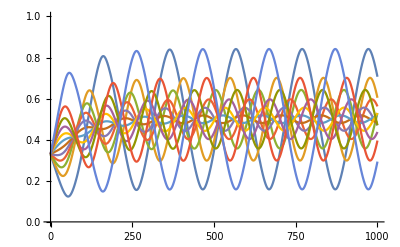

```mathematica
Plot[{v1series},{t,0,1000},PlotRange -> {0,1}]
```

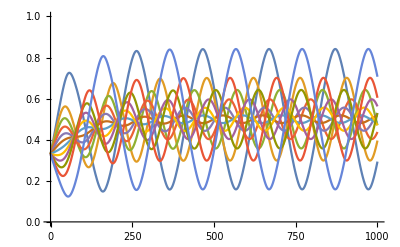

```mathematica
Plot[{v2series},{t,0,1000},PlotRange -> {0,1}]
```

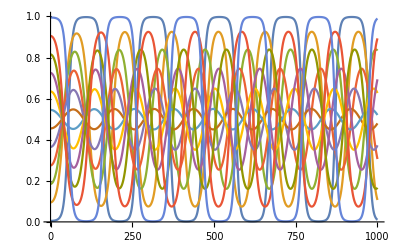

```mathematica
Plot[{useries},{t,0,1000},PlotRange -> {0,1}]
```

This this system results in a limit cycle regardless of the initial frequency of the symbiont. Next, I’ll show that the generalist host always goes extinct when its payoff is sufficiently low based on its parameter values. Note that for the fitness feedback system we found that the raw difference between specialist and generalist parameter values was no longer sufficient to fully explain whether the system cycled, or fixed for the generalist. To confirm, we made sure that the generalist goes extinct when it has a lower average payoff:

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[3000]+v2[3000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{}

```mathematica
PA=Simplify[ANT[0.9,0.31,0.3,10,0.1,1/2]];
```

```mathematica
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,10000},{u0, v10, v20}]
```

ParametricFunction[<>]

Now we’ll plot this system, while first just varying the initial frequency of the specialist host. We’ll begin with intermediate frequencies of all host types:

Now we will hold symbiont frequency steady and vary the initial frequency of only host 1:

```mathematica
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.33}}, {v10,0.005,0.995,0.09},{v20,{0.33}}, {vg0,{0.33}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

Now we’ll plot the frequency of hosts:

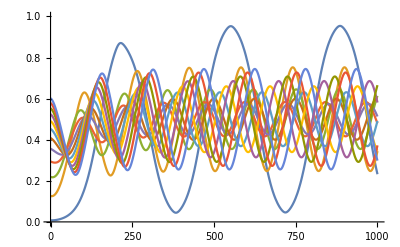

```mathematica
Plot[{v1series},{t,0,1000},PlotRange -> {0,1}]
```

And here we’ll plot the frequency of symbionts:

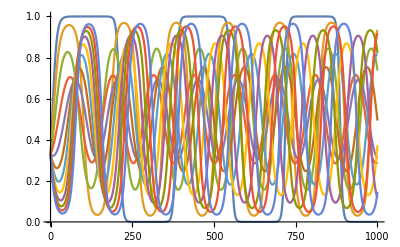

```mathematica
Plot[{useries},{t,0,1000},PlotRange -> {0,1}]
```

So any initial frequency of host 1 leads to a limit cycle.

We’ll check our result that generalists go extinct:

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[3000]+v2[3000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{}

As expected the generalists are excluded from the limit cycle. Next we vary the initial frequency of symbiont 2:

```mathematica
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.33}}, {v10,{0.33}},{v20,0.005,0.995,0.09}, {vg0,{0.33}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

Now we’ll plot the frequency of hosts:

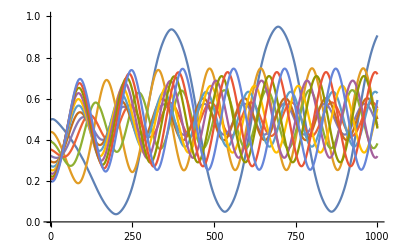

```mathematica
Plot[{v1series},{t,0,1000},PlotRange -> {0,1}]
```

Next the symbionts:

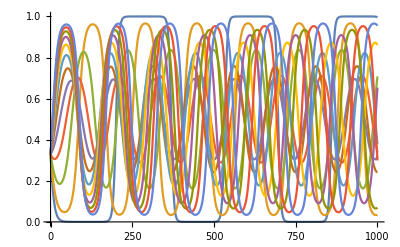

```mathematica
Plot[{useries},{t,0,1000},PlotRange -> {0,1}]
```

Once more we’ll check the frequency of generalists:

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[3000]+v2[3000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{}

As before generalists go extinct.

```mathematica
HostPayoffCheck[0.9,0.31,0.3,2,0.1,1/2]
```

{{0.00205782},{}}

```mathematica
PA=Simplify[ANT[0.9,0.31,0.3,2,0.1,1/2]];
```

```mathematica
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,20000},{u0, v10, v20}];
```

Finally, we’ll test the extreme cases when one match or mismatch is extremely likely to fix. These occur when generalists are nearly entirely absent, and hosts and symbiont parings are extremely frequent or infrequent:

```mathematica
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.005,0.995}}, {v10,{0.005,0.995}},{v20,{0.005,0.995}}, {vg0,{0.005}}]~Flatten~3;
```

```mathematica
interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

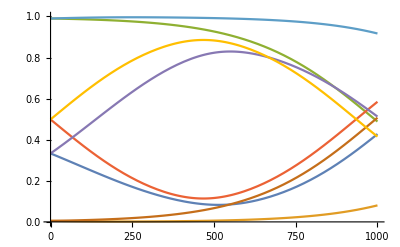

```mathematica
Plot[{v1series},{t,0,1000},PlotRange -> {0,1}]
```

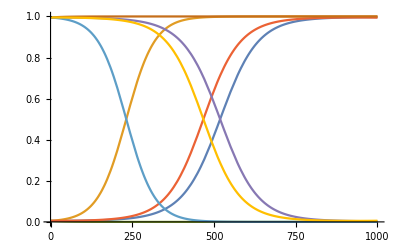

```mathematica
Plot[{useries},{t,0,1000},PlotRange -> {0,1}]
```

These cases too result in limit cycles. Let’s check the frequency of generalists.

```mathematica
(*If the sum of our two specialist's frequencies always equals 1, then there are no generalists*)
v1[t_]=v1series;
v2[t_]=v2series;
sum=v1[20000]+v2[20000];
(*Return any cases where the sum is not equal to 1 indicating presence of generalist:*)
Cases[sum,x_/;x≠ 1]
Clear[v1,v2]
```

{}

As before the generalists go extinct, all remaining hosts are specialists of one type or another.

What happens when generalist payoff exceeds specialist payoff? We will achieve this by raising the payoff of the generalist host:

```mathematica
HostPayoffCheck[0.9,0.7,0.3,2,0.1,1/2]
```

{{-0.0104684},{}}

```mathematica
PA=Simplify[ANT[0.9,0.7,0.3,2,0.1,1]];
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,20000},{u0, v10, v20}];
```

Well first explore this case while varying initial symbiont frequency:

```mathematica
ICs=Table[{u0,v10,v20},{u0,0.005,0.995,0.09}, {v10,{0.33}},{v20,{0.33}}]~Flatten~2;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

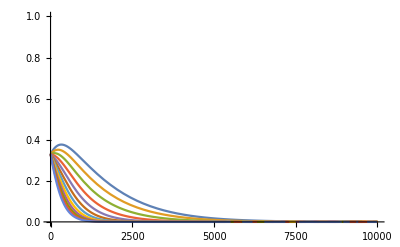

```mathematica
Plot[{v1series},{t,0,10000},PlotRange -> {0,1}]
```

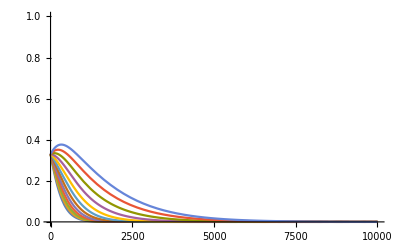

```mathematica
Plot[{v2series},{t,0,10000},PlotRange -> {0,1}]
```

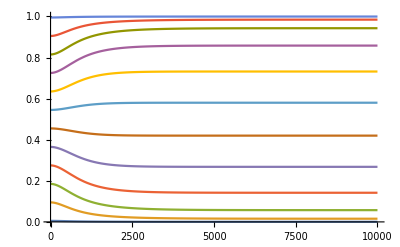

```mathematica
Plot[{useries},{t,0,10000},PlotRange -> {0,1}]
```

The generalist always fixes, and an intermediate symbiont frequency remains.

Now we’ll vary the initial frequency of host 1:

```mathematica
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.33}}, {v10,0.005,0.995,0.09},{v20,{0.05}},{vg0,{0.05}} ]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

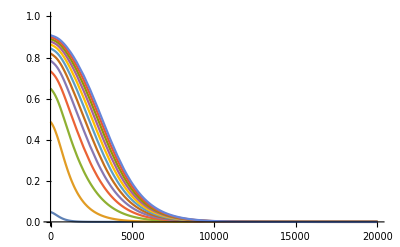

```mathematica
Plot[{v1series},{t,0,20000},PlotRange -> {0,1}]
```

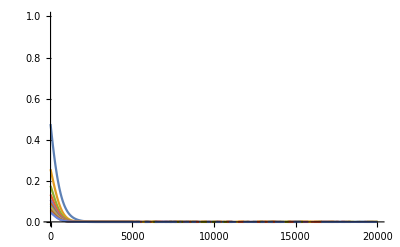

```mathematica
Plot[{v2series},{t,0,20000},PlotRange -> {0,1}]
```

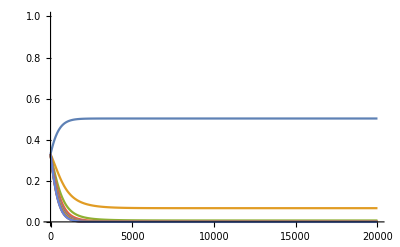

```mathematica
Plot[{useries},{t,0,20000},PlotRange -> {0,1}]
```

The symbiont frequency fixes at whatever value the population posessed when the specialists went extinct.

The same occurs in the case in which the frequency of the other specialist host varies.

We consider the cases that are highly favourable to fixation of the specialist, even when generalist payoff exceeds the specialists:

```mathematica
PA=Simplify[ANT[0.9,0.7,0.3,2,0.1,1/2]];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,20000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.005,0.995}}, {v10,{0.005,0.995}},{v20,{0.005,0.995}},{vg0,{0.005}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

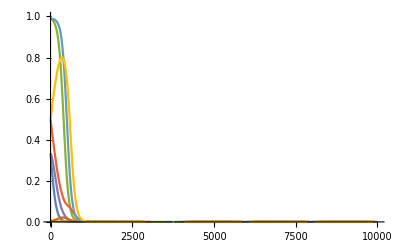

```mathematica
Plot[{v1series},{t,0,10000},PlotRange -> {0,1}]
```

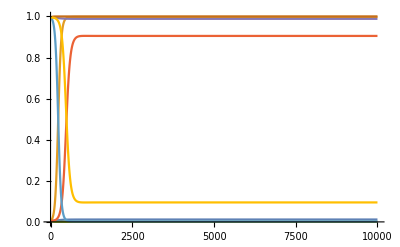

```mathematica
Plot[{useries},{t,0,10000},PlotRange -> {0,1}]
```

Finally, we consider strengthening the fitness feedback, which is analagous to the generalist payoff over the average specialist host payoff. Note we return to values of α, fα, and αg that would have previously resulted in a limit cycle. But now, the value of the fitness feedback constant b, is 1:

```mathematica
HostPayoffCheck[0.9,0.31,0.3,2,0.1,1]
```

{{-0.001976},{}}

Now, the generalists outcompete the specialists.

```mathematica
PA=Simplify[ANT[0.9,0.31,0.3,2,0.1,1]];(*With these parameters average specialist payoff exceeds the generalist payoff.*)
Ans=ParametricNDSolveValue[PA,{u[t],v1[t],v2[t]},{t,0,40000},{u0, v10, v20}];
ICs=Table[{u0,v10/(v10+v20+vg0),v20/(v10+v20+vg0)},{u0,{0.005,0.995}}, {v10,{0.005,0.995}},{v20,{0.005,0.995}},{vg0,{0.005}}]~Flatten~3;

interpolatingfunctions=Ans@@@ICs;
(*Host 1 frequencies are the second column of the interpolating function matrix. The symbiont is column 1, specialist 2 is column 3*)
v1series =interpolatingfunctions[[All,2]];
useries = interpolatingfunctions[[All,1]];
v2series = interpolatingfunctions[[All,3]];
```

```mathematica
|
```

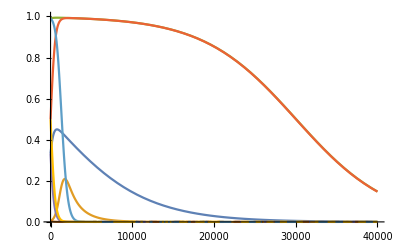

```mathematica
Plot[{v1series},{t,0,40000},PlotRange -> {0,1}]
```

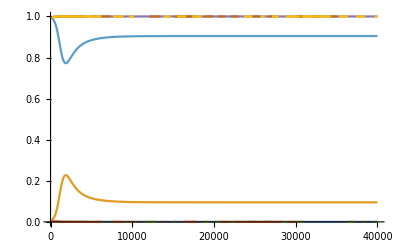

```mathematica
Plot[{useries},{t,0,40000},PlotRange -> {0,1}]
```

Stronger feedback leads to generalists outcompeting specialists.